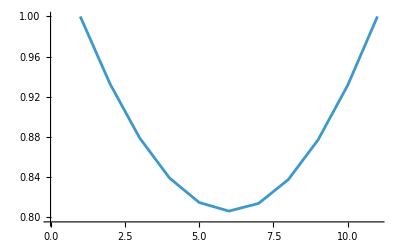

```mathematica
u0=1;
uN=1;
n=10;
a0=0;b0=Pi/2;
h=(b0-a0)/n;
x=Subdivide[a0,b0,n+1];
a=1/h^2-1/(2*h);
b=-2/h^2;
c=1/h^2+1/(2*h);
A=SparseArray[{{i_,j_}/;j==i-1->a,{i_,j_}/;j==i->b,{i_,j_}/;j==i+1->c},{n-1,n-1}];
f=Sin/@x;
rhs=f[[2;;n]];
rhs[[1]]=rhs[[1]]-a*u0;
rhs[[-1]]=rhs[[-1]]-c*uN;
uInner=LinearSolve[A,rhs];
u=Join[{u0},uInner,{uN}];
ListLinePlot[u]
```